```mathematica
RandomInteger[1,20]
```

{1,0,1,0,1,1,1,0,0,0,1,1,0,1,0,0,1,1,1,1}

```mathematica
TuringMachine[2506,{1,RandomInteger[1,10]},10]
```

{{{1,1,0},{0,0,1,0,1,1,1,1,1,1}},{{2,2,1},{1,0,1,0,1,1,1,1,1,1}},{{1,1,0},{1,1,1,0,1,1,1,1,1,1}},{{2,10,-1},{0,1,1,0,1,1,1,1,1,1}},{{1,1,0},{0,1,1,0,1,1,1,1,1,0}},{{2,2,1},{1,1,1,0,1,1,1,1,1,0}},{{1,3,2},{1,0,1,0,1,1,1,1,1,0}},{{2,2,1},{1,0,0,0,1,1,1,1,1,0}},{{1,1,0},{1,1,0,0,1,1,1,1,1,0}},{{2,10,-1},{0,1,0,0,1,1,1,1,1,0}},{{1,9,-2},{0,1,0,0,1,1,1,1,1,1}}}

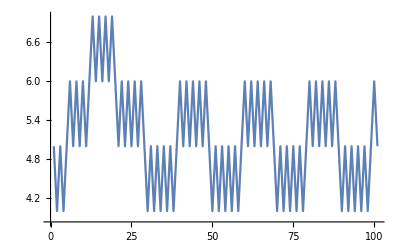

```mathematica
ListLinePlot[Total/@Last/@TuringMachine[2506,{1,RandomInteger[1,10]},100]]
```

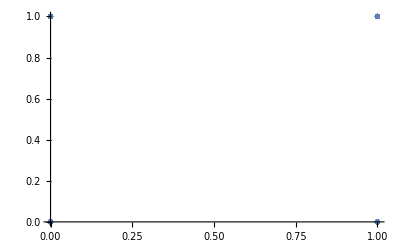

```mathematica
ListPlot[Last/@TuringMachine[2506,{1,RandomInteger[1,2]},100]]
```

```mathematica
ListLinePlot[Total/@Last/@TuringMachine[2506,{1,RandomInteger[1,10]},100]]
```

Get::noopen: Cannot open MechanicalSystems`Modeler2D`.

Needs::nocont: Context MechanicalSystems`Modeler2D` was not created when Needs was evaluated.

$Failed

Get::noopen: Cannot open MechanicalSystems`Modler2D`.

$Failed

```mathematica
YXfromAB[a_,b_]:={
d=0.9;
x = (-b^2 + a^2 + d^2)/(2*d);
y = Sqrt[a^2-x^2];
x,y
}
```

{0.866667,0.498888}

```mathematica
g = Graphics[{Line[{#,{0,0}}],Line[{#,{d,0}}]}]&;
p = g[YXfromAB[#1,#2]]&
```

g[YXfromAB[#1,#2]]&

```mathematica
Line
```

```mathematica
tm = Last/@TuringMachine[2506,{1,RandomInteger[1,2]},10]
```

{{1,1},{0,1},{0,0},{1,0},{1,1},{0,1},{0,0},{1,0},{1,1},{0,1},{0,0}}

```mathematica
{{0,0},{1,0},{1,1},{0,1},{0,0},{1,0},{1,1},{0,1},{0,0},{1,0},{1,1}}
```

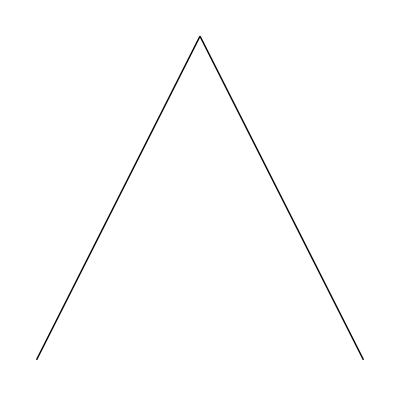
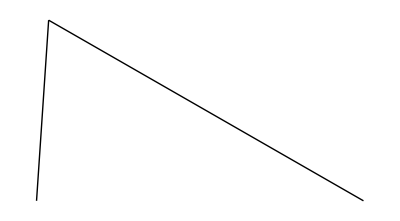
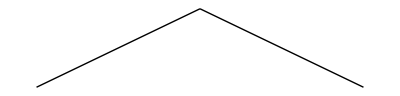
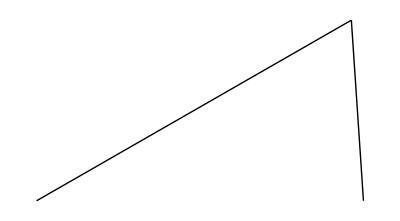
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[p[tm[[i,1]]*0.5+0.5,tm[[i,2]]*0.5+0.5],{i,9}]
```

```mathematica
tm[[3,2]]
```

0

```mathematica
<->
```

```mathematica
state =
```